```mathematica
worlddata=Import["https://covid.ourworldindata.org/data/owid-covid-data.csv"];
```

```mathematica
(*names={"Japan","Taiwan","Australia","United States","United Kingdom","India","France","Germany","Italy","New Zealand","Brazil","South Korea","Sweden","Thailand","China"};*)
(*names={"Japan","Taiwan","Australia","United States","United Kingdom","India","Italy","New Zealand","South Korea","Sweden","China"};*)
(*names={"Japan","Taiwan","Malaysia","Thailand","Vietnam","India","Indonesia","Mongolia","Singapore","Philippines","South Korea","China"};
namesLabel={"日本","台湾","マレーシア","タイ","ベトナム","インド","インドネシア","モンゴル","シンガポール","フィリピン","韓国","中国"}.08;
namesLabel=names;*)
```

```mathematica
names={"Japan"};
namesLabel=names;
```

```mathematica
font="Helvetica Neue";
fontsize=12;
```

```mathematica
startdate={2020,4,20};
enddate={2021,8,30};
startdateObj=DateObject[startdate];
date=4;
newDeathsSmoothed=10;
newDeathsSmoothedPerMillion=16;
newCasesSmoothedPerMillion=13;
newCasesSmoothed=7;
newCases=6;
kmax=Length[names];
dataTmp=Table[Cases[worlddata,x_?(#1[[3]]==names[[k]]&)][[All,{date,newDeathsSmoothedPerMillion,newCasesSmoothedPerMillion}]],{k,1,kmax}];
data=Table[DeleteCases[dataTmp[[k]],x_?(DateObject[#1[[1]]]<startdateObj&)],{k,1,kmax}];
```

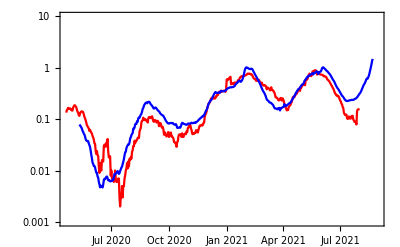

```mathematica
k=1;
d=21;
Show[
DateListLogPlot[Table[data[[k,i,2]] ,{i,1,Length[data[[k]]]}],DatePlus[DateObject[startdate],0],PlotStyle->{Red},
PlotLegends->Style["newCasesSmoothedPerMillion",Red],
DateTicksFormat->{"MonthShort"},
FrameStyle->Directive[fontsize,Black,FontFamily->font],Frame->True,
PlotRange->{{startdate,enddate},{0.001,10}}],
DateListLogPlot[ 
Table[0.02data[[k,i,3]] ,{i,1,Length[data[[k]]]}],DatePlus[DateObject[startdate],d],FrameTicks->{{Automatic,None},Automatic},
PlotStyle->{Blue},PlotLegends->Style["newDeathsSmoothedPerMillion",Blue]]
]
```